# Practical 2 (a) Rahul Chopra | BSc(H) Computer Science | Sem - IV | 20211449 Secant Method

## Question 1 :

x0=1

x1=2

Nmax=20

eps=1/1000000

f[x]:=Cos[x]

In 1th number of iterations the root is:1.5649

Estimated error is:0.435096

In 2th number of iterations the root is:1.57098

Estimated error is:0.0060742

In 3th number of iterations the root is:1.5708

Estimated error is:0.000182249

Return[1.5708]

Root is:1.5708

Estimated error is:1.02185×10^-9

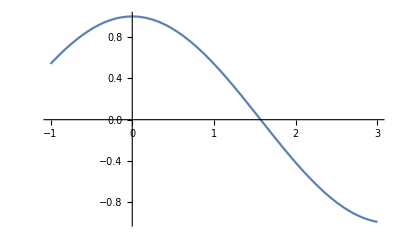

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x];
Print["f[x]:=",f[x]];
For[i=1,1≤Nmax,i++,
x2=N[x1-(f[x]/. x->x1)*(x1-x0)/((f[x]/. x->x1)-(f[x]/. x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2;];
Print["In ",i,"th number of iterations the root is:",x2];
Print["Estimated error is:",Abs[x1-x0]]];
Print["Root is:",x2];
Print["Estimated error is:",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```

## Question 2 :

x0=1

x1=2

Nmax=20

epsilon=1/1000000

f[x]:=1-5 x+x^3

In 1th number of iterations the root is:2.5

Estimated error is:0.5

In 2th number of iterations the root is:2.09756

Estimated error is:0.402439

In 3th number of iterations the root is:2.12134

Estimated error is:0.0237786

In 4th number of iterations the root is:2.12859

Estimated error is:0.0072456

In 5th number of iterations the root is:2.12842

Estimated error is:0.000166952

Return[2.12842]

Root is:2.12842

Estimated error is:8.77361×10^-7

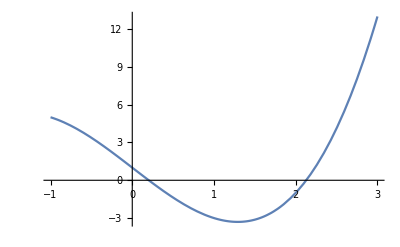

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=x^3-5x+1;
Print["f[x]:=",f[x]];
For[i=1,1≤Nmax,i++,
x2=N[x1-(f[x]/. x->x1)*(x1-x0)/((f[x]/. x->x1)-(f[x]/. x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2;];
Print["In ",i,"th number of iterations the root is:",x2];
Print["Estimated error is:",Abs[x1-x0]]];
Print["Root is:",x2];
Print["Estimated error is:",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```

## Question 3 :

x0=1

x1=2

Nmax=20

epsilon=1/1000000

f[x]:=-ⅇ^x x+Cos[x]

In 1th number of iterations the root is:0.832673

Estimated error is:1.16733

In 2th number of iterations the root is:0.728779

Estimated error is:0.103894

In 3th number of iterations the root is:0.562401

Estimated error is:0.166377

In 4th number of iterations the root is:0.524782

Estimated error is:0.0376189

In 5th number of iterations the root is:0.518014

Estimated error is:0.00676874

In 6th number of iterations the root is:0.517759

Estimated error is:0.0002547

In 7th number of iterations the root is:0.517757

Estimated error is:1.50138×10^-6

Return[0.517757]

Root is:0.517757

Estimated error is:3.22103×10^-10

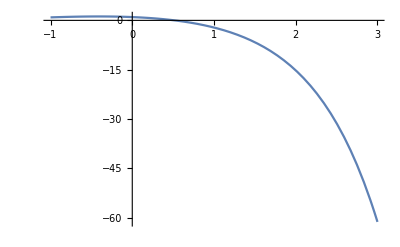

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x]-x*Exp[x];
Print["f[x]:=",f[x]];
For[i=1,1≤Nmax,i++,
x2=N[x1-(f[x]/. x->x1)*(x1-x0)/((f[x]/. x->x1)-(f[x]/. x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2;];
Print["In ",i,"th number of iterations the root is:",x2];
Print["Estimated error is:",Abs[x1-x0]]];
Print["Root is:",x2];
Print["Estimated error is:",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```